# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

mass leptons MM!=0, box diagrams with GAUGE=1

Confronto con:
- EW_MM_naive per d=4 -> OK
-Nar per d (box photons and born Z) CON SEMPLIFICAZIONE CARICHE PRIMA DEL CALCOLO DELLE TRACCE

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
(*Neglect[MM] = Neglect[MM2] = 0;*)
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0(*,MM->0,MM2->0,*),MD->0,MD2->0,S+T+U->2 MM2}
```

{MU→0,MU2→0,MD→0,MD2→0,S+T+U→2 MM2}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

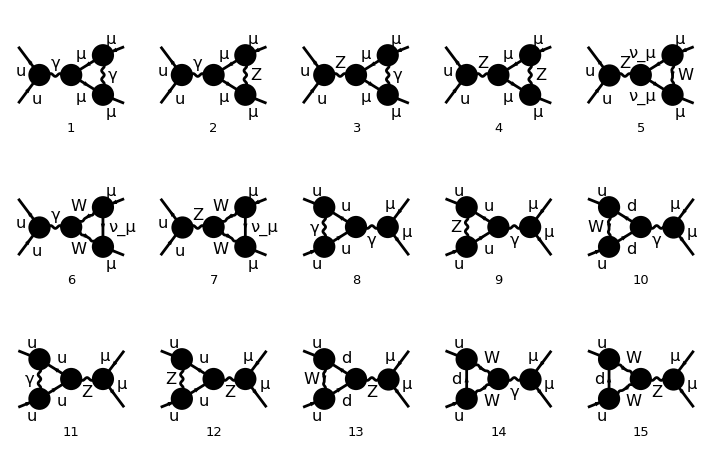

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

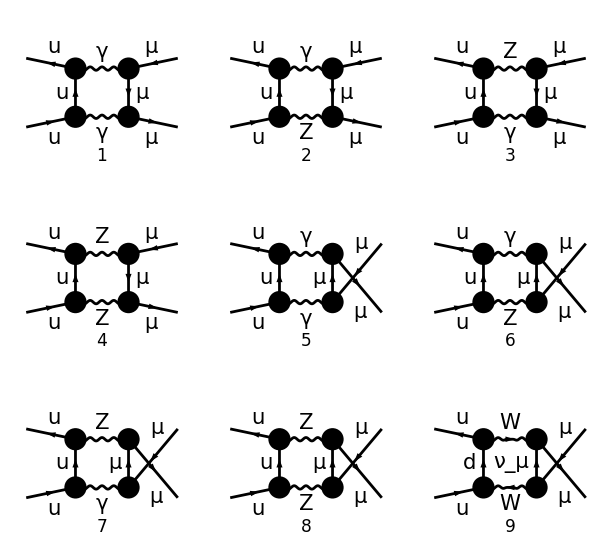

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

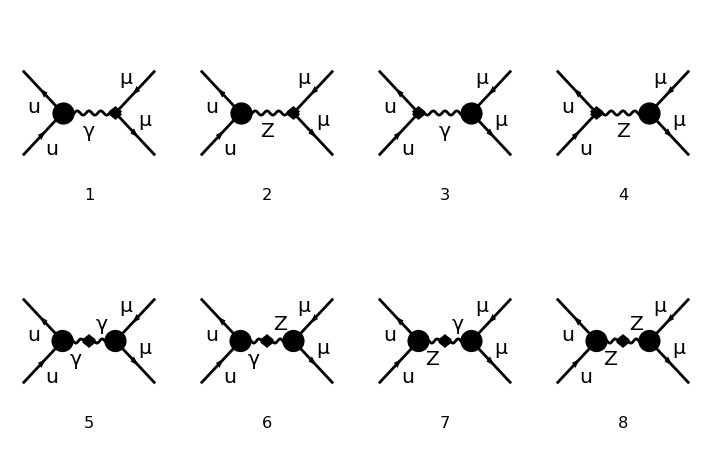

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[2][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[3][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
(*tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];*)
```

```mathematica
(*confronto Nar*)
tboxzz=tboxzz/.{Q1->-(Q1-P1)}//.{-P1-P2+K2->-K1,P1+P2-K2->K1}
uboxzz=uboxzz/.{Q1->(Q1-P2)}//.2P2-Q1->Q1//.Q1-K1-K2->-Q1+P1+P2//.PropagatorDenominator[Q1-K1,x_]->PropagatorDenominator[-Q1+K1,x]//.PropagatorDenominator[Q1-P2,x_]->PropagatorDenominator[-Q1+P2,x]
```

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[-(p1)+q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,MM].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).v[k1,MM] FeynAmpDenominator[1/(p1-q1)^2,1/(-MZ2+(p1+p2-q1)^2),1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[p2-q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,MM].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).v[k1,MM] FeynAmpDenominator[1/(p2-q1)^2,1/(-MZ2+(p1+p2-q1)^2),1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.NonCommutative[DiracMatrix[Index[Lorentz,bn1_]],ChiralityProjector[n_]]->NonCommutative[ChiralityProjector[n],DiracMatrix[Index[Lorentz,bn1]]]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(ⅈ EL QUl om_-.ga[Lorbn1]+ⅈ EL QUr om_+.ga[Lorbn1]).u[p1,0]],CONJ[ū[k1,MM].(ⅈ EL QLl om_-.ga[Lorbn2]+ⅈ EL QLr om_+.ga[Lorbn2]).v[k2,MM]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Propagators

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
bornpropag2
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p1-q1)^2 (q1)^2 (-MM2+(q1-k1)^2))

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p2-q1)^2 (q1)^2 (-MM2+(q1-k1)^2))

SP[Lorbn1,Lorbn2]/(k1+k2)^2

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] = -4 I myEps[a1,a2,a3,a4];
myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=MM2;
SP/:SP[K1,K1]:=MM2;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2-MM2;
SP/: SP[P1,K1]:=(MM2-T)/2;
SP/: SP[P2,K2]:=(MM2-T)/2; 
SP/:SP[P1,K2]:=(MM2-U)/2; SP/:SP[P2,K1]:=(MM2-U)/2;
```

```mathematica
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracMatrix[b],y]/;Head[b]=!=FourMomentum;
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracSlash[b],y]/;Head[b]===FourMomentum;
```

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=MM2*TR[x,y];
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=MM2*TR[x,y];
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
```

```mathematica
LARINtot:= traceff4[x___,G5,y___]:>LARIN[ traceff4[x,G5,y] ];
```

```mathematica
LARIN[expr_]:=Module[{ris,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12},
a1 = Index[Lorentz,Unique["x"]];
a2 = Index[Lorentz,Unique["x"]];
a3 = Index[Lorentz,Unique["x"]];
a4 = Index[Lorentz,Unique["x"]];
a5 = Index[Lorentz,Unique["x"]];
a6 = Index[Lorentz,Unique["x"]];
a7= Index[Lorentz,Unique["x"]];
a8 = Index[Lorentz,Unique["x"]];
a9 = Index[Lorentz,Unique["x"]];
a10 = Index[Lorentz,Unique["x"]];
a11 = Index[Lorentz,Unique["x"]];
a12 = Index[Lorentz,Unique["x"]];

pos = Position[ expr, G5];
Which[Length[pos]===1,
pos1 = Position[ expr, G5][[1,1]];
ris = I/24 fg51 myEps[a1,a2,a3,a4]*ReplacePart[expr,pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]] ],
Length[pos]===2,
pos1 = Position[ expr, G5][[1,1]];
pos2 = Position[ expr, G5][[2,1]];
ris = (I/24)^2 fg52 myEps[a1,a2,a3,a4]*myEps[a5,a6,a7,a8]*ReplacePart[expr,{pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]],
pos2->Sequence[DiracMatrix[a5],DiracMatrix[a6],DiracMatrix[a7],DiracMatrix[a8]]} ],
Length[pos]===3,
pos1 = Position[ expr, G5][[1,1]];
pos2 = Position[ expr, G5][[2,1]];
pos3 = Position[ expr, G5][[3,1]];
(*cambiare MYEPS in myEps per verificare i prodotti con 3 levicivita,ovvero conta l'ordine dei prodotti?*)
ris = (I/24)^3 fg53 myEps[a1,a2,a3,a4]*myEps[a5,a6,a7,a8]*myEps[a9,a10,a11,a12]*ReplacePart[expr,{pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]],
pos2->Sequence[DiracMatrix[a5],DiracMatrix[a6],DiracMatrix[a7],DiracMatrix[a8]],pos3->Sequence[DiracMatrix[a9],DiracMatrix[a10],DiracMatrix[a11],DiracMatrix[a12]]} ]
];

ris					   
];
```

```mathematica
(*semplificazione propagatore stato f*)
SEMPLtr={traceff4[a___,p[MM+DiracSlash[b__]],c___]/;OddQ[Count[traceff4[a,p[MM+DiracSlash[b]],c],DiracMatrix|DiracSlash,{2},Heads->True]]->traceff4[a,DiracSlash[b],c],
traceff4[a___,p[MM+DiracSlash[b__]],c___]/;EvenQ[Count[traceff4[a,p[MM+DiracSlash[b]],c],DiracMatrix|DiracSlash,{2},Heads->True]]->traceff4[a,MM,c]};
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{i,tr1i,tr2i,tr3i,tr4i,tr1f,tr2f,tr3f,tr4f,tracciai,tracciaf,chii,chff,omi,omf},

(*Prova traceff con mom k1 e p1 >0 v vbar->p-m uubar->p+m*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,1,b___]:=traceff4[a,b];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

(*stato i*)
omi=Count[statoi[[1]],_ChiralityProjector,Infinity];
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}];
tr2i=Map[Distribute,1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
tr2i=tr2i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)

tr3i=Collect[Collect[tr2i,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4i=tr3i//.TR->myTr;

Print["stato i ",1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
omf=Count[statof[[1]],_ChiralityProjector,Infinity];
tr1f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.SEMPLtr;
tr2f=Flatten[Map[Distribute,1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]];

tr2f=tr2f*chargetot[[2]]//.List->Plus//Simplify;(*prova*)

tr3f=Collect[Collect[tr2f,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4f=tr3f//.TR->myTr;

Print["stato f ",1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr4i,tr4f}]

];
```

```mathematica
(*stato i*)
omi=Count[stati[[1]],_ChiralityProjector,Infinity];
tr1i=Table[traceff4[stati[[i]]/.List->Sequence],{i,1,Length[stati]}];
tr2i=Map[Distribute,1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
tr2i=tr2i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)
```

```mathematica
(*stato f*)
omf=Count[statf[[1]],_ChiralityProjector,Infinity];
tr1f=Table[traceff4[statf[[i]]/.List->Sequence],{i,1,Length[statf]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.SEMPLtr;
tr2f=Flatten[Map[Distribute,1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]];

tr2f=tr2f*chargetot[[2]]//.List->Plus//Simplify;(*prova*)
tr3f=Collect[Collect[tr2f,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4f=tr3f//.TR->myTr;
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_,conjbornchains_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbi2=tbi(*Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List*);(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
stati=stati//.con ChiralityProjector[n_]->ChiralityProjector[-n];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[tbf[[i]]/.MM+DiracSlash[a__]->p[MM+DiracSlash[a]]//.List->f,{i,1,Length[tbf]}],Plus->Sequence,{3},Heads->True]//.f->List;
tbf3=DeleteCases[tbf2,0,1];
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
statf=statf//.con ChiralityProjector[n_]->ChiralityProjector[-n];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

#### CHARGES

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->MM2,SP[K1,K1]->MM2,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->S/2, SP[K1,K2]->S/2-MM2, SP[P1,K1]->(MM2-T)/2, SP[P2,K2]->(MM2-T)/2, SP[P1,K2]->(MM2-U)/2, SP[P2,K1]->(MM2-U)/2};
```

```mathematica
(*per calcolare altri box con photon/Z(caso boxtt o incrociato boxuu) o W(boxuu) basta cambiare la cariche, essendo le tracce della stessa tipologia*)
```

```mathematica
(* PER CARICHE DI ALTRI DIAGRAMMI: selezionare i diagrammi tboxzz e uboxzz, runnare fermiontrace per avere chi/chf (a differenza del caso senza larin qui non si cancellano tracce con om+om- quindi le cariche ci sono tutte) *)
```

```mathematica
(*fermiontrace[tboxzz,conjbornchains];*)
```

trace closed fermion loop(if any): {}

```mathematica
(*chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL}
Table[chI[i]=chargetot[[1,i]],{i,1,Length[chargetot[[1]]]}];
Table[chF[i]=chargetot[[2,i]],{i,1,Length[chargetot[[2]]]}];
Table[CHARGE[i1,i2]={chI[i1]*chF[i2]},{i1,1,Length[chargetot[[1]]]},{i2,1,Length[chargetot[[2]]]}];*)
```

#### amplitudes

```mathematica
boxtt=traces[fermiontrace[tboxzz,conjbornchains][[1]],fermiontrace[tboxzz,conjbornchains][[2]]]//.MYEPS->myEps;
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]]}

stato f {{1/8 (traceff4[MM,ga[Lor4],1-G5,MM,ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,MM,ga[Lor2],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1-G5,MM,ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,MM,ga[Lor2],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1-G5,MM,ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,MM,ga[Lor2],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1-G5,MM,ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,MM,ga[Lor2],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1+G5,MM,ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,MM,ga[Lor2],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1+G5,MM,ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,MM,ga[Lor2],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1+G5,MM,ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,MM,ga[Lor2],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor4],1+G5,MM,ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,MM,ga[Lor2],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]])}}

```mathematica
boxuu=traces[fermiontrace[uboxzz,conjbornchains][[1]],fermiontrace[uboxzz,conjbornchains][[2]]]//.MYEPS->myEps;
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]]}

stato f {{1/8 (traceff4[MM,ga[Lor2],1-G5,MM,ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,MM,ga[Lor4],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1-G5,MM,ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,MM,ga[Lor4],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1-G5,MM,ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,MM,ga[Lor4],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1-G5,MM,ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,MM,ga[Lor4],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1+G5,MM,ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,MM,ga[Lor4],1-G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1+G5,MM,ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,MM,ga[Lor4],1-G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1+G5,MM,ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,MM,ga[Lor4],1+G5,-MM,1+G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]])},{1/8 (traceff4[MM,ga[Lor2],1+G5,MM,ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]]+traceff4[MM,ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,MM,ga[Lor4],1+G5,-MM,1-G5,ga[Lorbn2]]+traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]])}}

## Simplifications

```mathematica
(*regole di sostituzione dei denominatori e regole inverse PER CONFRONTO NAR*)
SOST={-MZ2+(P2+Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2+Q1)^2->DMZGQ1P2,
-MW2+(P2+Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2+Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2+Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2+Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2+Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2+Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2+Q1)^2->-DMZGQ1P2,
MZ2-(P2+Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2+Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2+Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2+Q1)^2->-DMWGQ1P2,
MW2-(P2+Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2+Q1-K1-K2)^2->-DMWGQ1P2K1K2,
-MZ2+(P1+P2-Q1)^2->DMZQ1P1P2,MZ2-(P1+P2-Q1)^2->-DMZQ1P1P2,
-MZ2+Q1^2->DMZQ1,MZ2-Q1^2->-DMZQ1,

-MM2+(Q1-K1)^2->DMMQ1K1,
-MM2+(-Q1+K1)^2->DMMQ1K1,
-MM2+(-Q1+K2)^2->DMMQ1K2,
(P1+P2-Q1)->Sqrt[DQ1P1P2],


-MM2+(P2-Q1-K2)^2->DMMQ1P2K2,
-MM2+(P2-Q1-K1)^2->DMMQ1P2K1,
MM2-(P2-Q1-K2)^2->-DMMQ1P2K2,
MM2-(P2-Q1-K1)^2->-DMMQ1P2K1,
(P2-Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2+Q1)->Sqrt[DQ1P2],
(P2-Q1)->Sqrt[DmQ1P2],
(P1-Q1)->Sqrt[DQ1P1],
(K1+K2)->Sqrt[DK1K2],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

SOSTINV={DMZQ1P2->-MZ2+(P2+Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2+Q1)^2,
DMWQ1P2->-MW2+(P2+Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2+Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2+Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2+Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2+Q1-K1-K2)^2,

DQ1P2K1K2->(P2+Q1-K1-K2)^2,
DMMQ1P2K2->-MM2+(P2+Q1-K2)^2,
DMMQ1P2K1->-MM2+(P2+Q1-K1)^2,
DQ1P2->(P2+Q1)^2,
DQ1P1->(-P1+Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};
```

### box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
```

#### myEps

```mathematica
Tepsi=iep*tnumerat*bornpropag2//.SOST//Expand;
```

```mathematica
Teps=ParallelSum[Tepsi[[i]]*fep[[j]]//Expand,{i,1,Length[Tepsi]},{j,1,Length[fep]}];
```

#### NO myEps

```mathematica
Tneps=Collect[inep*fnep*bornpropag2*tnumerat//.SOST//ExpandNumerator,SP[__],Simplify];
```

```mathematica
amplT=Teps+Tneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.{MM->0,MM2->0}//Expand;
```

### box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Uepsi=iepu*bornpropag2*unumerat//.SOST//Expand;
```

```mathematica
Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}];
```

#### NO myEps

```mathematica
Uneps=Collect[inepu*fnepu*bornpropag2*unumerat//.SOST//ExpandNumerator,SP[__],Simplify];
```

```mathematica
amplU=Ueps+Uneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//Expand;
```

## confronto NAr

```mathematica
not={(*fg52->1,*)im->I,s13->-2SP[P1,K1],s23->-2SP[P2,K1],s12->2 SP[P1,P2],ml->MM,LlZ->el /(SW CW),UuZ->el /(SW CW),
Llph->QL el,Uuph->QU el,gVl->(I3L-2QL SW2),gVu->(I3U-2QU SW2),gAl->I3L,gAu->I3U,mZ2->MZ2,k1->FourMomentum[Internal,1],
p1->FourMomentum[Incoming,1],p4->FourMomentum[Outgoing,2],p2->FourMomentum[Incoming,2],p3->FourMomentum[Outgoing,1],n->d};
```

```mathematica
J[A1,n1_,n2_,n3_,n4_]->1/((k1^2)^n1 ((k1-p1)^2)^n2 ((k1-p1-p2)^2)^n3 ((k1-p3)^2-ml^2)^n4)
J[A2,n1_,n2_,n3_,n4_]->1/((k1^2)^n1 ((k1-p2)^2)^n2 ((k1-p1-p2)^2)^n3 ((k1-p3)^2-ml^2)^n4)
```

J[A1,n1_,n2_,n3_,n4_]→(k1^2)^-n1 ((k1-p1)^2)^-n2 ((k1-p1-p2)^2)^-n3 (-ml^2+(k1-p3)^2)^-n4

J[A2,n1_,n2_,n3_,n4_]→(k1^2)^-n1 ((k1-p2)^2)^-n2 ((k1-p1-p2)^2)^-n3 (-ml^2+(k1-p3)^2)^-n4

```mathematica
F1Zsq1=+J[A1,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+30/(-mZ2+s12)*n*s23*fg52+30/(-mZ2+s12)*n*s12*fg52-16/(-mZ2+s12)*n^2*s23*fg52-16/(-mZ2+s12)*n^2*s12*fg52+2/(-mZ2+s12)*n^3*s23*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A1,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23+16/(-mZ2+s12)*s12-6/(-mZ2+s12)*n*s23-6/(-mZ2+s12)*n*s12)+J[A1,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-216/(-mZ2+s12)*s23*fg52-432/(-mZ2+s12)*s13*fg52-216/(-mZ2+s12)*s12*fg52+192/(-mZ2+s12)*n*ml^2*fg52+150/(-mZ2+s12)*n*s23*fg52+330/(-mZ2+s12)*n*s13*fg52+120/(-mZ2+s12)*n*s12*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-32/(-mZ2+s12)*n^2*s23*fg52-80/(-mZ2+s12)*n^2*s13*fg52-16/(-mZ2+s12)*n^2*s12*fg52+2/(-mZ2+s12)*n^3*s23*fg52+6/(-mZ2+s12)*n^3*s13*fg52)+J[A1,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23-24/(-mZ2+s12)*s12+2/(-mZ2+s12)*n*s23-2/(-mZ2+s12)*n*s13+8/(-mZ2+s12)*n*s12)+J[A1,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+432/(-mZ2+s12)*s13*fg52-192/(-mZ2+s12)*n*ml^2*fg52-30/(-mZ2+s12)*n*s23*fg52-330/(-mZ2+s12)*n*s13*fg52+30/(-mZ2+s12)*n*s12*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+16/(-mZ2+s12)*n^2*s23*fg52+80/(-mZ2+s12)*n^2*s13*fg52-16/(-mZ2+s12)*n^2*s12*fg52-2/(-mZ2+s12)*n^3*s23*fg52-6/(-mZ2+s12)*n^3*s13*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A1,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s23+16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s23+2/(-mZ2+s12)*n*s13-6/(-mZ2+s12)*n*s12)+J[A1,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s12*fg52-180/(-mZ2+s12)*n*s23*fg52-210/(-mZ2+s12)*n*s12*fg52+48/(-mZ2+s12)*n^2*s23*fg52+64/(-mZ2+s12)*n^2*s12*fg52-4/(-mZ2+s12)*n^3*s23*fg52-6/(-mZ2+s12)*n^3*s12*fg52)+J[A1,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23-24/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s23+10/(-mZ2+s12)*n*s12)+J[A1,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s23^2*fg52-168/(-mZ2+s12)*s13*s23*fg52-48/(-mZ2+s12)*s12*s23*fg52-120/(-mZ2+s12)*s12*s13*fg52-24/(-mZ2+s12)*s12^2*fg52+20/(-mZ2+s12)*n*s23^2*fg52+116/(-mZ2+s12)*n*s13*s23*fg52+10/(-mZ2+s12)*n*s12*s23*fg52+106/(-mZ2+s12)*n*s12*s13*fg52-10/(-mZ2+s12)*n*s12^2*fg52-4/(-mZ2+s12)*n^2*s23^2*fg52-20/(-mZ2+s12)*n^2*s13*s23*fg52+8/(-mZ2+s12)*n^2*s12*s23*fg52-28/(-mZ2+s12)*n^2*s12*s13*fg52+12/(-mZ2+s12)*n^2*s12^2*fg52-2/(-mZ2+s12)*n^3*s12*s23*fg52+2/(-mZ2+s12)*n^3*s12*s13*fg52-2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A1,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s23*ml^2+8/(-mZ2+s12)*s23^2-8/(-mZ2+s12)*s13*s23-16/(-mZ2+s12)*s12*ml^2-8/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s23^2-4/(-mZ2+s12)*n*s13*s23-2/(-mZ2+s12)*n*s12*s23-2/(-mZ2+s12)*n*s12*s13+2/(-mZ2+s12)*n*s12^2)+J[A1,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s13*fg52-192/(-mZ2+s12)*n*ml^2*fg52-180/(-mZ2+s12)*n*s23*fg52-180/(-mZ2+s12)*n*s13*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+48/(-mZ2+s12)*n^2*s23*fg52+48/(-mZ2+s12)*n^2*s13*fg52-4/(-mZ2+s12)*n^3*s23*fg52-4/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23-8/(-mZ2+s12)*s13+4/(-mZ2+s12)*n*s23+4/(-mZ2+s12)*n*s13)+J[A1,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-216/(-mZ2+s12)*s13*fg52+192/(-mZ2+s12)*n*ml^2*fg52+30/(-mZ2+s12)*n*s23*fg52+210/(-mZ2+s12)*n*s13*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-16/(-mZ2+s12)*n^2*s23*fg52-64/(-mZ2+s12)*n^2*s13*fg52+2/(-mZ2+s12)*n^3*s23*fg52+6/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23+24/(-mZ2+s12)*s13-6/(-mZ2+s12)*n*s23-10/(-mZ2+s12)*n*s13)+J[A1,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s13*fg52+216/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s23*fg52-180/(-mZ2+s12)*n*s13*fg52-120/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s23*fg52+48/(-mZ2+s12)*n^2*s13*fg52+16/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s23*fg52-4/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s23-8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s23+4/(-mZ2+s12)*n*s13-8/(-mZ2+s12)*n*s12)+J[A1,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+24/(-mZ2+s12)*s23^2*fg52-96/(-mZ2+s12)*s13*s23*fg52-120/(-mZ2+s12)*s13^2*fg52+384/(-mZ2+s12)*s12*ml^2*fg52+24/(-mZ2+s12)*s12*s23*fg52+144/(-mZ2+s12)*s12*s13*fg52-20/(-mZ2+s12)*n*s23^2*fg52+56/(-mZ2+s12)*n*s13*s23*fg52+76/(-mZ2+s12)*n*s13^2*fg52-224/(-mZ2+s12)*n*s12*ml^2*fg52-50/(-mZ2+s12)*n*s12*s23*fg52-150/(-mZ2+s12)*n*s12*s13*fg52+4/(-mZ2+s12)*n^2*s23^2*fg52-8/(-mZ2+s12)*n^2*s13*s23*fg52-12/(-mZ2+s12)*n^2*s13^2*fg52+32/(-mZ2+s12)*n^2*s12*ml^2*fg52+20/(-mZ2+s12)*n^2*s12*s23*fg52+52/(-mZ2+s12)*n^2*s12*s13*fg52-2/(-mZ2+s12)*n^3*s12*s23*fg52-6/(-mZ2+s12)*n^3*s12*s13*fg52)+J[A1,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23*ml^2-8/(-mZ2+s12)*s23^2-16/(-mZ2+s12)*s13*ml^2-24/(-mZ2+s12)*s13^2-24/(-mZ2+s12)*s12*s23-32/(-mZ2+s12)*s12*s13+4/(-mZ2+s12)*n*s23^2+8/(-mZ2+s12)*n*s13*s23+4/(-mZ2+s12)*n*s13^2+10/(-mZ2+s12)*n*s12*s23+14/(-mZ2+s12)*n*s12*s13)+J[A1,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-30/(-mZ2+s12)*n*s13*fg52+16/(-mZ2+s12)*n^2*s13*fg52-2/(-mZ2+s12)*n^3*s13*fg52)+J[A1,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s13+6/(-mZ2+s12)*n*s13)+J[A1,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s13*fg52+180/(-mZ2+s12)*n*s13*fg52-30/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s13*fg52+16/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s13*fg52-2/(-mZ2+s12)*n^3*s12*fg52)+J[A1,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A1,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s13*s23*fg52+120/(-mZ2+s12)*s13^2*fg52+24/(-mZ2+s12)*s12*s13*fg52+20/(-mZ2+s12)*n*s13*s23*fg52-76/(-mZ2+s12)*n*s13^2*fg52+40/(-mZ2+s12)*n*s12*s13*fg52-4/(-mZ2+s12)*n^2*s13*s23*fg52+12/(-mZ2+s12)*n^2*s13^2*fg52-28/(-mZ2+s12)*n^2*s12*s13*fg52+4/(-mZ2+s12)*n^3*s12*s13*fg52)+J[A1,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s13*ml^2+8/(-mZ2+s12)*s13*s23+24/(-mZ2+s12)*s13^2+24/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s13*s23-4/(-mZ2+s12)*n*s13^2-8/(-mZ2+s12)*n*s12*s13)+J[A1,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s12*fg52)+J[A1,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s12)+J[A1,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+24/(-mZ2+s12)*s12*s23*fg52+288/(-mZ2+s12)*s12*s13*fg52+24/(-mZ2+s12)*s12^2*fg52-20/(-mZ2+s12)*n*s12*s23*fg52-216/(-mZ2+s12)*n*s12*s13*fg52+10/(-mZ2+s12)*n*s12^2*fg52+4/(-mZ2+s12)*n^2*s12*s23*fg52+52/(-mZ2+s12)*n^2*s12*s13*fg52-12/(-mZ2+s12)*n^2*s12^2*fg52-4/(-mZ2+s12)*n^3*s12*s13*fg52+2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A1,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+32/(-mZ2+s12)*s13*s23-16/(-mZ2+s12)*s12*ml^2-8/(-mZ2+s12)*s12*s23+8/(-mZ2+s12)*s12^2+4/(-mZ2+s12)*n*s12*s23+8/(-mZ2+s12)*n*s12*s13-2/(-mZ2+s12)*n*s12^2)+J[A1,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s12*s13*s23*fg52-72/(-mZ2+s12)*s12*s13^2*fg52-24/(-mZ2+s12)*s12^2*s13*fg52+20/(-mZ2+s12)*n*s12*s13*s23*fg52+36/(-mZ2+s12)*n*s12*s13^2*fg52-10/(-mZ2+s12)*n*s12^2*s13*fg52-4/(-mZ2+s12)*n^2*s12*s13*s23*fg52-4/(-mZ2+s12)*n^2*s12*s13^2*fg52+12/(-mZ2+s12)*n^2*s12^2*s13*fg52-2/(-mZ2+s12)*n^3*s12^2*s13*fg52)+J[A1,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32/(-mZ2+s12)*s13^2*s23+16/(-mZ2+s12)*s12*s13*ml^2+8/(-mZ2+s12)*s12*s13*s23-8/(-mZ2+s12)*s12*s13^2-8/(-mZ2+s12)*s12^2*s13-4/(-mZ2+s12)*n*s12*s13*s23-4/(-mZ2+s12)*n*s12*s13^2+2/(-mZ2+s12)*n*s12^2*s13);
```

```mathematica
F1Zsq2=+J[A2,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-240/(-mZ2+s12)*s13*fg52-240/(-mZ2+s12)*s12*fg52+170/(-mZ2+s12)*n*s13*fg52+170/(-mZ2+s12)*n*s12*fg52-36/(-mZ2+s12)*n^2*s13*fg52-36/(-mZ2+s12)*n^2*s12*fg52+2/(-mZ2+s12)*n^3*s13*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A2,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A2,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-192/(-mZ2+s12)*s23*fg52+24/(-mZ2+s12)*s13*fg52+264/(-mZ2+s12)*s12*fg52+192/(-mZ2+s12)*n*ml^2*fg52+190/(-mZ2+s12)*n*s23*fg52+10/(-mZ2+s12)*n*s13*fg52-160/(-mZ2+s12)*n*s12*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-60/(-mZ2+s12)*n^2*s23*fg52-12/(-mZ2+s12)*n^2*s13*fg52+24/(-mZ2+s12)*n^2*s12*fg52+6/(-mZ2+s12)*n^3*s23*fg52+2/(-mZ2+s12)*n^3*s13*fg52)+J[A2,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12+2/(-mZ2+s12)*n*s23-2/(-mZ2+s12)*n*s13-8/(-mZ2+s12)*n*s12)+J[A2,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+192/(-mZ2+s12)*s23*fg52+240/(-mZ2+s12)*s13*fg52-240/(-mZ2+s12)*s12*fg52-192/(-mZ2+s12)*n*ml^2*fg52-190/(-mZ2+s12)*n*s23*fg52-170/(-mZ2+s12)*n*s13*fg52+170/(-mZ2+s12)*n*s12*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+60/(-mZ2+s12)*n^2*s23*fg52+36/(-mZ2+s12)*n^2*s13*fg52-36/(-mZ2+s12)*n^2*s12*fg52-6/(-mZ2+s12)*n^3*s23*fg52-2/(-mZ2+s12)*n^3*s13*fg52+2/(-mZ2+s12)*n^3*s12*fg52)+J[A2,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-2/(-mZ2+s12)*n*s23-6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A2,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+216/(-mZ2+s12)*s13*fg52+456/(-mZ2+s12)*s12*fg52-180/(-mZ2+s12)*n*s13*fg52-350/(-mZ2+s12)*n*s12*fg52+48/(-mZ2+s12)*n^2*s13*fg52+84/(-mZ2+s12)*n^2*s12*fg52-4/(-mZ2+s12)*n^3*s13*fg52-6/(-mZ2+s12)*n^3*s12*fg52)+J[A2,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A2,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-168/(-mZ2+s12)*s13*s23*fg52-24/(-mZ2+s12)*s13^2*fg52-360/(-mZ2+s12)*s12*s23*fg52+192/(-mZ2+s12)*s12*s13*fg52+216/(-mZ2+s12)*s12^2*fg52+116/(-mZ2+s12)*n*s13*s23*fg52+20/(-mZ2+s12)*n*s13^2*fg52+246/(-mZ2+s12)*n*s12*s23*fg52-130/(-mZ2+s12)*n*s12*s13*fg52-150/(-mZ2+s12)*n*s12^2*fg52-20/(-mZ2+s12)*n^2*s13*s23*fg52-4/(-mZ2+s12)*n^2*s13^2*fg52-48/(-mZ2+s12)*n^2*s12*s23*fg52+28/(-mZ2+s12)*n^2*s12*s13*fg52+32/(-mZ2+s12)*n^2*s12^2*fg52+2/(-mZ2+s12)*n^3*s12*s23*fg52-2/(-mZ2+s12)*n^3*s12*s13*fg52-2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A2,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s13*ml^2+8/(-mZ2+s12)*s13*s23-8/(-mZ2+s12)*s13^2+16/(-mZ2+s12)*s12*ml^2+8/(-mZ2+s12)*s12*s23+8/(-mZ2+s12)*s12^2+4/(-mZ2+s12)*n*s13*s23+4/(-mZ2+s12)*n*s13^2+2/(-mZ2+s12)*n*s12*s23+2/(-mZ2+s12)*n*s12*s13-2/(-mZ2+s12)*n*s12^2)+J[A2,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*ml^2*fg52+216/(-mZ2+s12)*s23*fg52+216/(-mZ2+s12)*s13*fg52-192/(-mZ2+s12)*n*ml^2*fg52-180/(-mZ2+s12)*n*s23*fg52-180/(-mZ2+s12)*n*s13*fg52+32/(-mZ2+s12)*n^2*ml^2*fg52+48/(-mZ2+s12)*n^2*s23*fg52+48/(-mZ2+s12)*n^2*s13*fg52-4/(-mZ2+s12)*n^3*s23*fg52-4/(-mZ2+s12)*n^3*s13*fg52)+J[A2,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s23+8/(-mZ2+s12)*s13-4/(-mZ2+s12)*n*s23-4/(-mZ2+s12)*n*s13)+J[A2,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-288/(-mZ2+s12)*ml^2*fg52-456/(-mZ2+s12)*s23*fg52-240/(-mZ2+s12)*s13*fg52+192/(-mZ2+s12)*n*ml^2*fg52+350/(-mZ2+s12)*n*s23*fg52+170/(-mZ2+s12)*n*s13*fg52-32/(-mZ2+s12)*n^2*ml^2*fg52-84/(-mZ2+s12)*n^2*s23*fg52-36/(-mZ2+s12)*n^2*s13*fg52+6/(-mZ2+s12)*n^3*s23*fg52+2/(-mZ2+s12)*n^3*s13*fg52)+J[A2,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-24/(-mZ2+s12)*s23-16/(-mZ2+s12)*s13+10/(-mZ2+s12)*n*s23+6/(-mZ2+s12)*n*s13)+J[A2,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+216/(-mZ2+s12)*s23*fg52-216/(-mZ2+s12)*s13*fg52-264/(-mZ2+s12)*s12*fg52-180/(-mZ2+s12)*n*s23*fg52+180/(-mZ2+s12)*n*s13*fg52+160/(-mZ2+s12)*n*s12*fg52+48/(-mZ2+s12)*n^2*s23*fg52-48/(-mZ2+s12)*n^2*s13*fg52-24/(-mZ2+s12)*n^2*s12*fg52-4/(-mZ2+s12)*n^3*s23*fg52+4/(-mZ2+s12)*n^3*s13*fg52)+J[A2,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8/(-mZ2+s12)*s23-8/(-mZ2+s12)*s13-24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s23+4/(-mZ2+s12)*n*s13+8/(-mZ2+s12)*n*s12)+J[A2,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-120/(-mZ2+s12)*s23^2*fg52-96/(-mZ2+s12)*s13*s23*fg52+24/(-mZ2+s12)*s13^2*fg52+384/(-mZ2+s12)*s12*ml^2*fg52+384/(-mZ2+s12)*s12*s23*fg52+264/(-mZ2+s12)*s12*s13*fg52+76/(-mZ2+s12)*n*s23^2*fg52+56/(-mZ2+s12)*n*s13*s23*fg52-20/(-mZ2+s12)*n*s13^2*fg52-224/(-mZ2+s12)*n*s12*ml^2*fg52-290/(-mZ2+s12)*n*s12*s23*fg52-190/(-mZ2+s12)*n*s12*s13*fg52-12/(-mZ2+s12)*n^2*s23^2*fg52-8/(-mZ2+s12)*n^2*s13*s23*fg52+4/(-mZ2+s12)*n^2*s13^2*fg52+32/(-mZ2+s12)*n^2*s12*ml^2*fg52+72/(-mZ2+s12)*n^2*s12*s23*fg52+40/(-mZ2+s12)*n^2*s12*s13*fg52-6/(-mZ2+s12)*n^3*s12*s23*fg52-2/(-mZ2+s12)*n^3*s12*s13*fg52)+J[A2,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23*ml^2+24/(-mZ2+s12)*s23^2-16/(-mZ2+s12)*s13*ml^2+8/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*s23+24/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s23^2-8/(-mZ2+s12)*n*s13*s23-4/(-mZ2+s12)*n*s13^2-14/(-mZ2+s12)*n*s12*s23-10/(-mZ2+s12)*n*s12*s13)+J[A2,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+240/(-mZ2+s12)*s23*fg52-170/(-mZ2+s12)*n*s23*fg52+36/(-mZ2+s12)*n^2*s23*fg52-2/(-mZ2+s12)*n^3*s23*fg52)+J[A2,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16/(-mZ2+s12)*s23-6/(-mZ2+s12)*n*s23)+J[A2,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s23*fg52+240/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s23*fg52-170/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s23*fg52+36/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s23*fg52-2/(-mZ2+s12)*n^3*s12*fg52)+J[A2,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s23+16/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s23-6/(-mZ2+s12)*n*s12)+J[A2,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+120/(-mZ2+s12)*s23^2*fg52-24/(-mZ2+s12)*s13*s23*fg52-456/(-mZ2+s12)*s12*s23*fg52-76/(-mZ2+s12)*n*s23^2*fg52+20/(-mZ2+s12)*n*s13*s23*fg52+320/(-mZ2+s12)*n*s12*s23*fg52+12/(-mZ2+s12)*n^2*s23^2*fg52-4/(-mZ2+s12)*n^2*s13*s23*fg52-68/(-mZ2+s12)*n^2*s12*s23*fg52+4/(-mZ2+s12)*n^3*s12*s23*fg52)+J[A2,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16/(-mZ2+s12)*s23*ml^2-24/(-mZ2+s12)*s23^2-8/(-mZ2+s12)*s13*s23-24/(-mZ2+s12)*s12*s23+4/(-mZ2+s12)*n*s23^2+4/(-mZ2+s12)*n*s13*s23+8/(-mZ2+s12)*n*s12*s23)+J[A2,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-216/(-mZ2+s12)*s12*fg52+180/(-mZ2+s12)*n*s12*fg52-48/(-mZ2+s12)*n^2*s12*fg52+4/(-mZ2+s12)*n^3*s12*fg52)+J[A2,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s12)+J[A2,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(+288/(-mZ2+s12)*s12*s23*fg52+24/(-mZ2+s12)*s12*s13*fg52-216/(-mZ2+s12)*s12^2*fg52-216/(-mZ2+s12)*n*s12*s23*fg52-20/(-mZ2+s12)*n*s12*s13*fg52+150/(-mZ2+s12)*n*s12^2*fg52+52/(-mZ2+s12)*n^2*s12*s23*fg52+4/(-mZ2+s12)*n^2*s12*s13*fg52-32/(-mZ2+s12)*n^2*s12^2*fg52-4/(-mZ2+s12)*n^3*s12*s23*fg52+2/(-mZ2+s12)*n^3*s12^2*fg52)+J[A2,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32/(-mZ2+s12)*s13*s23+16/(-mZ2+s12)*s12*ml^2+8/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-8/(-mZ2+s12)*n*s12*s23-4/(-mZ2+s12)*n*s12*s13+2/(-mZ2+s12)*n*s12^2)+J[A2,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*(-72/(-mZ2+s12)*s12*s23^2*fg52-24/(-mZ2+s12)*s12*s13*s23*fg52+216/(-mZ2+s12)*s12^2*s23*fg52+36/(-mZ2+s12)*n*s12*s23^2*fg52+20/(-mZ2+s12)*n*s12*s13*s23*fg52-150/(-mZ2+s12)*n*s12^2*s23*fg52-4/(-mZ2+s12)*n^2*s12*s23^2*fg52-4/(-mZ2+s12)*n^2*s12*s13*s23*fg52+32/(-mZ2+s12)*n^2*s12^2*s23*fg52-2/(-mZ2+s12)*n^3*s12^2*s23*fg52)+J[A2,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+32/(-mZ2+s12)*s13*s23^2-16/(-mZ2+s12)*s12*s23*ml^2+8/(-mZ2+s12)*s12*s23^2-8/(-mZ2+s12)*s12*s13*s23+8/(-mZ2+s12)*s12^2*s23+4/(-mZ2+s12)*n*s12*s23^2+4/(-mZ2+s12)*n*s12*s13*s23-2/(-mZ2+s12)*n*s12^2*s23);
```

```mathematica
F1Psq1=+J[A1,-1,1,1,1]*im*borncf*Uuph^3*Llph^3*(+16+16*s12^(-1)*s23-6*n*s12^(-1)*s23-6*n)+J[A1,0,0,1,1]*im*borncf*Uuph^3*Llph^3*(-24-8*s12^(-1)*s23+2*n*s12^(-1)*s23-2*n*s12^(-1)*s13+8*n)+J[A1,0,1,0,1]*im*borncf*Uuph^3*Llph^3*(+16-16*s12^(-1)*s23+6*n*s12^(-1)*s23+2*n*s12^(-1)*s13-6*n)+J[A1,0,1,1,0]*im*borncf*Uuph^3*Llph^3*(-24-8*s12^(-1)*s23+4*n*s12^(-1)*s23+10*n)+J[A1,0,1,1,1]*im*borncf*Uuph^3*Llph^3*(-16*s12^(-1)*s23*ml^2+8*s12^(-1)*s23^2-8*s12^(-1)*s13*s23-16*ml^2-8*s13-8*s12-4*n*s12^(-1)*s23^2-4*n*s12^(-1)*s13*s23-2*n*s23-2*n*s13+2*n*s12)+J[A1,1,-1,1,1]*im*borncf*Uuph^3*Llph^3*(-8*s12^(-1)*s23-8*s12^(-1)*s13+4*n*s12^(-1)*s23+4*n*s12^(-1)*s13)+J[A1,1,0,0,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23+24*s12^(-1)*s13-6*n*s12^(-1)*s23-10*n*s12^(-1)*s13)+J[A1,1,0,1,0]*im*borncf*Uuph^3*Llph^3*(+24+8*s12^(-1)*s23-8*s12^(-1)*s13-4*n*s12^(-1)*s23+4*n*s12^(-1)*s13-8*n)+J[A1,1,0,1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23*ml^2-8*s12^(-1)*s23^2-16*s12^(-1)*s13*ml^2-24*s12^(-1)*s13^2-24*s23-32*s13+4*n*s12^(-1)*s23^2+8*n*s12^(-1)*s13*s23+4*n*s12^(-1)*s13^2+10*n*s23+14*n*s13)+J[A1,1,1,-1,1]*im*borncf*Uuph^3*Llph^3*(-16*s12^(-1)*s13+6*n*s12^(-1)*s13)+J[A1,1,1,0,0]*im*borncf*Uuph^3*Llph^3*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A1,1,1,0,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s13*ml^2+8*s12^(-1)*s13*s23+24*s12^(-1)*s13^2+24*s13-4*n*s12^(-1)*s13*s23-4*n*s12^(-1)*s13^2-8*n*s13)+J[A1,1,1,1,-1]*im*borncf*Uuph^3*Llph^3*(+8-4*n)+J[A1,1,1,1,0]*im*borncf*Uuph^3*Llph^3*(+32*s12^(-1)*s13*s23-16*ml^2-8*s23+8*s12+4*n*s23+8*n*s13-2*n*s12)+J[A1,1,1,1,1]*im*borncf*Uuph^3*Llph^3*(-32*s12^(-1)*s13^2*s23+16*s13*ml^2+8*s13*s23-8*s13^2-8*s12*s13-4*n*s13*s23-4*n*s13^2+2*n*s12*s13);

F1Psq2=+J[A2,-1,1,1,1]*im*borncf*Uuph^3*Llph^3*(-16-16*s12^(-1)*s13+6*n*s12^(-1)*s13+6*n)+J[A2,0,0,1,1]*im*borncf*Uuph^3*Llph^3*(+24+8*s12^(-1)*s13+2*n*s12^(-1)*s23-2*n*s12^(-1)*s13-8*n)+J[A2,0,1,0,1]*im*borncf*Uuph^3*Llph^3*(-16+16*s12^(-1)*s13-2*n*s12^(-1)*s23-6*n*s12^(-1)*s13+6*n)+J[A2,0,1,1,0]*im*borncf*Uuph^3*Llph^3*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A2,0,1,1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s13*ml^2+8*s12^(-1)*s13*s23-8*s12^(-1)*s13^2+16*ml^2+8*s23+8*s12+4*n*s12^(-1)*s13*s23+4*n*s12^(-1)*s13^2+2*n*s23+2*n*s13-2*n*s12)+J[A2,1,-1,1,1]*im*borncf*Uuph^3*Llph^3*(+8*s12^(-1)*s23+8*s12^(-1)*s13-4*n*s12^(-1)*s23-4*n*s12^(-1)*s13)+J[A2,1,0,0,1]*im*borncf*Uuph^3*Llph^3*(-24*s12^(-1)*s23-16*s12^(-1)*s13+10*n*s12^(-1)*s23+6*n*s12^(-1)*s13)+J[A2,1,0,1,0]*im*borncf*Uuph^3*Llph^3*(-24+8*s12^(-1)*s23-8*s12^(-1)*s13-4*n*s12^(-1)*s23+4*n*s12^(-1)*s13+8*n)+J[A2,1,0,1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23*ml^2+24*s12^(-1)*s23^2-16*s12^(-1)*s13*ml^2+8*s12^(-1)*s13^2+32*s23+24*s13-4*n*s12^(-1)*s23^2-8*n*s12^(-1)*s13*s23-4*n*s12^(-1)*s13^2-14*n*s23-10*n*s13)+J[A2,1,1,-1,1]*im*borncf*Uuph^3*Llph^3*(+16*s12^(-1)*s23-6*n*s12^(-1)*s23)+J[A2,1,1,0,0]*im*borncf*Uuph^3*Llph^3*(+16-8*s12^(-1)*s23+4*n*s12^(-1)*s23-6*n)+J[A2,1,1,0,1]*im*borncf*Uuph^3*Llph^3*(-16*s12^(-1)*s23*ml^2-24*s12^(-1)*s23^2-8*s12^(-1)*s13*s23-24*s23+4*n*s12^(-1)*s23^2+4*n*s12^(-1)*s13*s23+8*n*s23)+J[A2,1,1,1,-1]*im*borncf*Uuph^3*Llph^3*(-8+4*n)+J[A2,1,1,1,0]*im*borncf*Uuph^3*Llph^3*(-32*s12^(-1)*s13*s23+16*ml^2+8*s13-8*s12-8*n*s23-4*n*s13+2*n*s12)+J[A2,1,1,1,1]*im*borncf*Uuph^3*Llph^3*(+32*s12^(-1)*s13*s23^2-16*s23*ml^2+8*s23^2-8*s13*s23+8*s12*s23+4*n*s23^2+4*n*s13*s23-2*n*s12*s23);
```

```mathematica
SEMPL1[box_]:=Module[{soll,soll0,soll1,soll2},
soll=box//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.SOST//.{SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->MM2,SP[K1,K1]->MM2}//Expand;

soll0=soll//.SP[K1,Q1]->-1/2(DMMQ1K1-SP[Q1,Q1]);
If[FreeQ[soll0,DmQ1P2,Infinity],
soll1=soll0//.SP[P2,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P1]//.SP[P1,Q1]->-1/2(DQ1P1-SP[Q1,Q1]),
soll1=soll0//.SP[P1,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P2]//.SP[P2,Q1]->-1/2(DmQ1P2-SP[Q1,Q1])
];
soll2=Simplify[soll1//.sostituzione//.SOST,TimeConstraint->Infinity];
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

```mathematica
amplT=ParallelMap[SEMPL1,amplT];
amplU=ParallelMap[SEMPL1,amplU];
```

### Caso photon (box 2 photon + born photon)

```mathematica
DENOMT=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplT//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
DENOMU=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplU//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DQ1 DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DQ1)}

{1/(DMMQ1K1 DmQ1P2 DQ1 DQ1P1P2),1/(DmQ1P2 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DmQ1P2)}

```mathematica
ariT=Collect[amplT//.DK1K2->S//Expand,DENOMT,Simplify];
ariU=Collect[amplU//.DK1K2->S//Expand,DENOMU,Simplify];
```

```mathematica
F1p2=F1Psq1//.J[A1,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.SOST//.sostituzione;
F1p22=F1Psq2//.J[A2,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.SOST//.sostituzione;
```

```mathematica
DENOMTnar=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1p2//Expand]],_Integer|S |Pi,Infinity]], Length[#1]>Length[#2] &]];
DENOMUnar=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1p22//Expand]],_Integer|S |Pi,Infinity]], Length[#1]>Length[#2] &]];
```

```mathematica
narT=Collect[F1p2,DENOMTnar,Simplify]//.MASSES;
narU=Collect[F1p22,DENOMUnar,Simplify]//.MASSES;
```

```mathematica
Collect[ariT//Expand,DENOMT,Simplify]+Collect[ariU/.{T->U,U->T}/.{DmQ1P2->DQ1P1,DQ1P1->DmQ1P2}//Expand,DENOMT,Simplify]//Simplify
```

0

```mathematica
f[T_,U_]=amplTp+amplUp;
```

```mathematica
f[a,b]-f[b,a]//Expand
```

0

```mathematica
Collect[narT*nar+ariT*ari/.{U->2MM2-S-T}//Expand,DENOMT,Simplify]
Collect[narU*nar+ariU*ari/.{T->2MM2-S-U}//Expand,DENOMU,Simplify]
```

(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (-MM2+T) ((-8+3 d) DQ1-2 (-4+d) S+8 T))/(8 DMMQ1K1 DQ1P1 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (-MM2+T) ((-8+3 d) DQ1P1P2-2 (-4+d) S+8 T))/(8 DMMQ1K1 DQ1 DQ1P1 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 ((-4+d) MM2+(8-3 d) S-(-4+d) T))/(4 DMMQ1K1 DQ1P1 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-4+d) S-2 (-2+d) T))/(4 DQ1 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) T))/(8 DMMQ1K1 DQ1 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) T))/(8 DQ1 DQ1P1 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) T))/(8 DMMQ1K1 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) T))/(8 DQ1P1 DQ1P1P2 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (MM2-T) (16 MM2^2+(-8+3 d) S^2-32 MM2 T+8 S T+16 T^2))/(8 DMMQ1K1 DQ1 DQ1P1 DQ1P1P2 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) DQ1P1 S-8 S^2+3 d S^2+2 MM2 ((-2+d) S-8 T)+12 S T-2 d S T+16 T^2))/(8 DMMQ1K1 DQ1 DQ1P1P2 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (16 MM2^2+2 (-2+d) DMMQ1K1 S+2 (-2+d) MM2 S-8 S^2+3 d S^2-32 MM2 T+12 S T-2 d S T+16 T^2))/(8 DQ1 DQ1P1 DQ1P1P2 π^4 S)

(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (MM2-U) ((-8+3 d) DQ1-2 (-4+d) S+8 U))/(8 DMMQ1K1 DmQ1P2 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (MM2-U) ((-8+3 d) DQ1P1P2-2 (-4+d) S+8 U))/(8 DMMQ1K1 DmQ1P2 DQ1 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (-(-4+d) MM2+(-8+3 d) S+(-4+d) U))/(4 DMMQ1K1 DmQ1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-4+d) S-2 (-2+d) U))/(4 DQ1 DQ1P1P2 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) U))/(8 DMMQ1K1 DQ1 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) U))/(8 DmQ1P2 DQ1 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) U))/(8 DMMQ1K1 DQ1P1P2 π^4 S)-(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) MM2+(-8+3 d) S-2 (-2+d) U))/(8 DmQ1P2 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (MM2-U) (16 MM2^2+(-8+3 d) S^2-32 MM2 U+8 S U+16 U^2))/(8 DMMQ1K1 DmQ1P2 DQ1 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (2 (-2+d) DmQ1P2 S-8 S^2+3 d S^2+2 MM2 ((-2+d) S-8 U)+12 S U-2 d S U+16 U^2))/(8 DMMQ1K1 DQ1 DQ1P1P2 π^4 S)+(ⅈ el^6 (ari+16 borncf nar π^4) QL^3 QU^3 (16 MM2^2+2 (-2+d) DMMQ1K1 S+2 (-2+d) MM2 S-8 S^2+3 d S^2-32 MM2 U+12 S U-2 d S U+16 U^2))/(8 DmQ1P2 DQ1 DQ1P1P2 π^4 S)

### caso Z (box 2 photons and born Z)

```mathematica
amplT=ToExpression[Import["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/amplboxt.txt","List"]][[1]]//.SOST(*//.{fg51->1,fg52->1,fg53->1}*)//.(DK1K2-MZ2)->DMZK1K2//.(-DQ1+MM2+2Q1 K1-K1^2)->-DMMQ1K1//.(DQ1-MM2-2Q1 K1+K1^2)->DMMQ1K1//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)};
amplU=ToExpression[Import["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/amplboxu.txt","List"]][[1]]//.SOST(*//.{fg51->1,fg52->1,fg53->1}*)//.(DK1K2-MZ2)->DMZK1K2//.(-DQ1+MM2+2Q1 K1-K1^2)->-DMMQ1K1//.(DQ1-MM2-2Q1 K1+K1^2)->DMMQ1K1//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)};
```

```mathematica
DENOMT=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplT//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
DENOMU=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplU//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DQ1 DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DQ1)}

{1/(DMMQ1K1 DmQ1P2 DQ1 DQ1P1P2),1/(DmQ1P2 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DmQ1P2)}

```mathematica
ariTz=Collect[amplT//Expand,DENOMT,Simplify];
ariUz=Collect[amplU//Expand,DENOMU,Simplify];
```

```mathematica
F1zp2=F1Zsq1//.J[A1,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//Expand;
F1zp22=F1Zsq2//.J[A2,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//Expand;
```

```mathematica
DENOMTznar=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp2//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
DENOMUznar=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp22//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DQ1 DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DQ1)}

{1/(DMMQ1K1 DmQ1P2 DQ1 DQ1P1P2),1/(DmQ1P2 DQ1 DQ1P1P2),1/(DMMQ1K1 DQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DmQ1P2)}

```mathematica
narTz=Collect[F1zp2,DENOMTznar,Simplify];
narUz=Collect[F1zp22,DENOMUznar,Simplify];
```

```mathematica
totzT=Collect[narTz*nar+ariTz*ari//.DMZK1K2->-MZ2+S/.{U->2MM2-S-T}//.fg51->Sqrt[fg52]//Expand,DENOMT,Simplify];
totzU=Collect[narUz*nar+ariUz*ari//.DMZK1K2->-MZ2+S/.{T->2MM2-S-U}//.fg51->Sqrt[fg52]//Expand,DENOMU,Simplify];
```

```mathematica
Table[MemberQ[totzT[[i]],fg53,Infinity],{i,1,Length[totzT]}]
Table[MemberQ[totzU[[i]],fg53,Infinity],{i,1,Length[totzT]}]
```

{False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False}

```mathematica
coeffAN=Plus[ari,Times[32,borncf,nar,Power[Pi,4]]]
```

ari+32 borncf nar π^4

```mathematica
Table[MemberQ[totzT[[i]],coeffAN,Infinity],{i,1,Length[totzT]}]
Table[MemberQ[totzU[[i]],coeffAN,Infinity],{i,1,Length[totzU]}]
```

{True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True}

### caso box ph/Z born ph

```mathematica
A1:{sp[k1,k1],sp[k1-p1,k1-p1],sp[k1-p1-p2,k1-p1-p2]-mZ^2,sp[k1-p3,k1-p3]},A2:{sp[k1,k1],sp[k1-p2,k1-p2],sp[k1-p1-p2,k1-p1-p2]-mZ^2,sp[k1-p3,k1-p3]},A3:{sp[k1,k1]-mZ^2,sp[k1-p1,k1-p1],sp[k1-p1-p2,k1-p1-p2],sp[k1-p3,k1-p3]},A4:{sp[k1,k1]-mZ^2,sp[k1-p2,k1-p2],sp[k1-p1-p2,k1-p1-p2],sp[k1-p3,k1-p3]},
```

```mathematica
F1Psq1g=+J[A1,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-30*n*s12^(-1)*s13+16*n^2*s12^(-1)*s13-2*n^3*s12^(-1)*s13)+J[A1,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13+6*n*s12^(-1)*s13)+J[A1,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A1,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A1,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+48*s12^(-1)*s13+20*n*s12^(-1)*s13+60*n-24*n^2*s12^(-1)*s13-32*n^2+4*n^3*s12^(-1)*s13+4*n^3)+J[A1,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+32+16*s12^(-1)*s13-4*n*s12^(-1)*s13-12*n)+J[A1,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A1,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A1,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+48*s12^(-1)*s13*mZ^2+144*s12^(-1)*s13^2+432*s13+20*n*s12^(-1)*s13*mZ^2-96*n*s12^(-1)*s13^2+60*n*mZ^2-300*n*s13-24*n^2*s12^(-1)*s13*mZ^2+16*n^2*s12^(-1)*s13^2-32*n^2*mZ^2+64*n^2*s13+4*n^3*s12^(-1)*s13*mZ^2+4*n^3*mZ^2-4*n^3*s13)+J[A1,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16*s12^(-1)*s13*mZ^2+16*s12^(-1)*s13^2+32*mZ^2+16*s13-4*n*s12^(-1)*s13*mZ^2-12*n*mZ^2-4*n*s13)+J[A1,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-24+20*n-4*n^2)+J[A1,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8-4*n)+J[A1,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A1,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A1,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+48+48*s12^(-1)*s13-40*n*s12^(-1)*s13+20*n+8*n^2*s12^(-1)*s13-24*n^2+4*n^3)+J[A1,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16-16*s12^(-1)*s13+8*n*s12^(-1)*s13-4*n)+J[A1,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13*mZ^2-120*s13+20*n*s12^(-1)*s13*mZ^2-30*n*mZ^2+76*n*s13+30*n*s12-4*n^2*s12^(-1)*s13*mZ^2+16*n^2*mZ^2-12*n^2*s13-16*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A1,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2-32*s12^(-1)*s13^2-16*mZ^2-24*s13+16*s12-4*n*s12^(-1)*s13*mZ^2+6*n*mZ^2+4*n*s13-6*n*s12)+J[A1,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-30*n*s12^(-1)*s13+16*n^2*s12^(-1)*s13-2*n^3*s12^(-1)*s13)+J[A1,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13+6*n*s12^(-1)*s13)+J[A1,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A1,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A1,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-48*s12^(-1)*s13^2+48*s13-60*n*s12^(-1)*s13*mZ^2+16*n*s12^(-1)*s13^2+20*n*s13+32*n^2*s12^(-1)*s13*mZ^2-24*n^2*s13-4*n^3*s12^(-1)*s13*mZ^2+4*n^3*s13)+J[A1,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32*s12^(-1)*s13*mZ^2+16*s12^(-1)*s13^2+16*s13+12*n*s12^(-1)*s13*mZ^2-4*n*s13)+J[A1,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-24+20*n-4*n^2)+J[A1,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8-4*n)+J[A1,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13*mZ^2-120*s13+20*n*s12^(-1)*s13*mZ^2-30*n*mZ^2+76*n*s13+30*n*s12-4*n^2*s12^(-1)*s13*mZ^2+16*n^2*mZ^2-12*n^2*s13-16*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A1,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2-32*s12^(-1)*s13^2-16*mZ^2-24*s13+16*s12-4*n*s12^(-1)*s13*mZ^2+6*n*mZ^2+4*n*s13-6*n*s12)+J[A1,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-48*s12^(-1)*s13^2*mZ^2+48*s13*mZ^2+144*s13^2-30*n*s12^(-1)*s13*mZ^4+16*n*s12^(-1)*s13^2*mZ^2+20*n*s13*mZ^2-96*n*s13^2-30*n*s12*s13+16*n^2*s12^(-1)*s13*mZ^4-24*n^2*s13*mZ^2+16*n^2*s13^2+16*n^2*s12*s13-2*n^3*s12^(-1)*s13*mZ^4+4*n^3*s13*mZ^2-2*n^3*s12*s13)+J[A1,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13*mZ^4+16*s12^(-1)*s13^2*mZ^2+32*s12^(-1)*s13^3+16*s13*mZ^2+16*s13^2-16*s12*s13+6*n*s12^(-1)*s13*mZ^4-4*n*s13*mZ^2+6*n*s12*s13);
```

```mathematica
F1Psq2g=+J[A3,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-30*n*s12^(-1)*s13+16*n^2*s12^(-1)*s13-2*n^3*s12^(-1)*s13)+J[A3,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13+6*n*s12^(-1)*s13)+J[A3,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A3,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A3,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+48*s12^(-1)*s13+20*n*s12^(-1)*s13+60*n-24*n^2*s12^(-1)*s13-32*n^2+4*n^3*s12^(-1)*s13+4*n^3)+J[A3,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+32+16*s12^(-1)*s13-4*n*s12^(-1)*s13-12*n)+J[A3,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A3,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A3,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-48*s12^(-1)*s13^2+48*s13-60*n*s12^(-1)*s13*mZ^2+16*n*s12^(-1)*s13^2+20*n*s13+32*n^2*s12^(-1)*s13*mZ^2-24*n^2*s13-4*n^3*s12^(-1)*s13*mZ^2+4*n^3*s13)+J[A3,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32*s12^(-1)*s13*mZ^2+16*s12^(-1)*s13^2+16*s13+12*n*s12^(-1)*s13*mZ^2-4*n*s13)+J[A3,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24+20*n-4*n^2)+J[A3,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8-4*n)+J[A3,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A3,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A3,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+48+48*s12^(-1)*s13-40*n*s12^(-1)*s13+20*n+8*n^2*s12^(-1)*s13-24*n^2+4*n^3)+J[A3,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16-16*s12^(-1)*s13+8*n*s12^(-1)*s13-4*n)+J[A3,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13*mZ^2-120*s13+20*n*s12^(-1)*s13*mZ^2-30*n*mZ^2+76*n*s13+30*n*s12-4*n^2*s12^(-1)*s13*mZ^2+16*n^2*mZ^2-12*n^2*s13-16*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A3,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2-32*s12^(-1)*s13^2-16*mZ^2-24*s13+16*s12-4*n*s12^(-1)*s13*mZ^2+6*n*mZ^2+4*n*s13-6*n*s12)+J[A3,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-30*n*s12^(-1)*s13+16*n^2*s12^(-1)*s13-2*n^3*s12^(-1)*s13)+J[A3,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13+6*n*s12^(-1)*s13)+J[A3,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13+20*n*s12^(-1)*s13-30*n-4*n^2*s12^(-1)*s13+16*n^2-2*n^3)+J[A3,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+8*s12^(-1)*s13-4*n*s12^(-1)*s13+6*n)+J[A3,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+48*s12^(-1)*s13*mZ^2+144*s12^(-1)*s13^2+432*s13+20*n*s12^(-1)*s13*mZ^2-96*n*s12^(-1)*s13^2+60*n*mZ^2-300*n*s13-24*n^2*s12^(-1)*s13*mZ^2+16*n^2*s12^(-1)*s13^2-32*n^2*mZ^2+64*n^2*s13+4*n^3*s12^(-1)*s13*mZ^2+4*n^3*mZ^2-4*n^3*s13)+J[A3,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16*s12^(-1)*s13*mZ^2+16*s12^(-1)*s13^2+32*mZ^2+16*s13-4*n*s12^(-1)*s13*mZ^2-12*n*mZ^2-4*n*s13)+J[A3,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24+20*n-4*n^2)+J[A3,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8-4*n)+J[A3,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24*s12^(-1)*s13*mZ^2-120*s13+20*n*s12^(-1)*s13*mZ^2-30*n*mZ^2+76*n*s13+30*n*s12-4*n^2*s12^(-1)*s13*mZ^2+16*n^2*mZ^2-12*n^2*s13-16*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A3,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2-32*s12^(-1)*s13^2-16*mZ^2-24*s13+16*s12-4*n*s12^(-1)*s13*mZ^2+6*n*mZ^2+4*n*s13-6*n*s12)+J[A3,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-48*s12^(-1)*s13^2*mZ^2+48*s13*mZ^2+144*s13^2-30*n*s12^(-1)*s13*mZ^4+16*n*s12^(-1)*s13^2*mZ^2+20*n*s13*mZ^2-96*n*s13^2-30*n*s12*s13+16*n^2*s12^(-1)*s13*mZ^4-24*n^2*s13*mZ^2+16*n^2*s13^2+16*n^2*s12*s13-2*n^3*s12^(-1)*s13*mZ^4+4*n^3*s13*mZ^2-2*n^3*s12*s13)+J[A3,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13*mZ^4+16*s12^(-1)*s13^2*mZ^2+32*s12^(-1)*s13^3+16*s13*mZ^2+16*s13^2-16*s12*s13+6*n*s12^(-1)*s13*mZ^4-4*n*s13*mZ^2+6*n*s12*s13);
```

```mathematica
F1Psq3=+J[A4,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-240-240*s12^(-1)*s13+170*n*s12^(-1)*s13+170*n-36*n^2*s12^(-1)*s13-36*n^2+2*n^3*s12^(-1)*s13+2*n^3)+J[A4,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16-16*s12^(-1)*s13+6*n*s12^(-1)*s13+6*n)+J[A4,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A4,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A4,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-48+432*s12^(-1)*s13-300*n*s12^(-1)*s13+40*n+64*n^2*s12^(-1)*s13-8*n^2-4*n^3*s12^(-1)*s13)+J[A4,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+16*s12^(-1)*s13-4*n*s12^(-1)*s13+8*n)+J[A4,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A4,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A4,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-480*s12^(-1)*s13*mZ^2-48*s12^(-1)*s13^2-480*mZ^2+336*s13+384*s12+340*n*s12^(-1)*s13*mZ^2+16*n*s12^(-1)*s13^2+340*n*mZ^2-268*n*s13-284*n*s12-72*n^2*s12^(-1)*s13*mZ^2-72*n^2*mZ^2+64*n^2*s13+64*n^2*s12+4*n^3*s12^(-1)*s13*mZ^2+4*n^3*mZ^2-4*n^3*s13-4*n^3*s12)+J[A4,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32*s12^(-1)*s13*mZ^2-16*s12^(-1)*s13^2-32*mZ^2-16*s13+12*n*s12^(-1)*s13*mZ^2+12*n*mZ^2-4*n*s13-4*n*s12)+J[A4,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24+20*n-4*n^2)+J[A4,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8+4*n)+J[A4,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A4,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A4,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-480-48*s12^(-1)*s13+40*n*s12^(-1)*s13+340*n-8*n^2*s12^(-1)*s13-72*n^2+4*n^3)+J[A4,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32-16*s12^(-1)*s13+8*n*s12^(-1)*s13+12*n)+J[A4,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+24*s12^(-1)*s13*mZ^2+264*mZ^2+120*s13-120*s12-20*n*s12^(-1)*s13*mZ^2-190*n*mZ^2-76*n*s13+94*n*s12+4*n^2*s12^(-1)*s13*mZ^2+40*n^2*mZ^2+12*n^2*s13-24*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A4,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2+32*s12^(-1)*s13^2+24*mZ^2+40*s13-8*s12-4*n*s12^(-1)*s13*mZ^2-10*n*mZ^2+4*n*s13+10*n*s12)+J[A4,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-240-240*s12^(-1)*s13+170*n*s12^(-1)*s13+170*n-36*n^2*s12^(-1)*s13-36*n^2+2*n^3*s12^(-1)*s13+2*n^3)+J[A4,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16-16*s12^(-1)*s13+6*n*s12^(-1)*s13+6*n)+J[A4,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A4,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A4,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+432*s12^(-1)*s13*mZ^2+144*s12^(-1)*s13^2-48*mZ^2+336*s13+192*s12-300*n*s12^(-1)*s13*mZ^2-96*n*s12^(-1)*s13^2+40*n*mZ^2-172*n*s13-76*n*s12+64*n^2*s12^(-1)*s13*mZ^2+16*n^2*s12^(-1)*s13^2-8*n^2*mZ^2+8*n^2*s13-8*n^2*s12-4*n^3*s12^(-1)*s13*mZ^2+4*n^3*s13+4*n^3*s12)+J[A4,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16*s12^(-1)*s13*mZ^2-16*s12^(-1)*s13^2-16*mZ^2-16*s13-4*n*s12^(-1)*s13*mZ^2+8*n*mZ^2-4*n*s13-4*n*s12)+J[A4,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-24+20*n-4*n^2)+J[A4,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8+4*n)+J[A4,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+24*s12^(-1)*s13*mZ^2+264*mZ^2+120*s13-120*s12-20*n*s12^(-1)*s13*mZ^2-190*n*mZ^2-76*n*s13+94*n*s12+4*n^2*s12^(-1)*s13*mZ^2+40*n^2*mZ^2+12*n^2*s13-24*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A4,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2+32*s12^(-1)*s13^2+24*mZ^2+40*s13-8*s12-4*n*s12^(-1)*s13*mZ^2-10*n*mZ^2+4*n*s13+10*n*s12)+J[A4,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-240*s12^(-1)*s13*mZ^4-48*s12^(-1)*s13^2*mZ^2-240*mZ^4+336*s13*mZ^2+144*s13^2+384*s12*mZ^2+48*s12*s13-96*s12^2+170*n*s12^(-1)*s13*mZ^4+16*n*s12^(-1)*s13^2*mZ^2+170*n*mZ^4-268*n*s13*mZ^2-96*n*s13^2-284*n*s12*mZ^2-22*n*s12*s13+74*n*s12^2-36*n^2*s12^(-1)*s13*mZ^4-36*n^2*mZ^4+64*n^2*s13*mZ^2+16*n^2*s13^2+64*n^2*s12*mZ^2-4*n^2*s12*s13-20*n^2*s12^2+2*n^3*s12^(-1)*s13*mZ^4+2*n^3*mZ^4-4*n^3*s13*mZ^2-4*n^3*s12*mZ^2+2*n^3*s12*s13+2*n^3*s12^2)+J[A4,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13*mZ^4-16*s12^(-1)*s13^2*mZ^2+32*s12^(-1)*s13^3-16*mZ^4-16*s13*mZ^2+80*s13^2+48*s12*s13+6*n*s12^(-1)*s13*mZ^4+6*n*mZ^4-4*n*s13*mZ^2-4*n*s12*mZ^2+6*n*s12*s13+6*n*s12^2);
```

```mathematica
F1Psq4=+J[A2,-1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-240-240*s12^(-1)*s13+170*n*s12^(-1)*s13+170*n-36*n^2*s12^(-1)*s13-36*n^2+2*n^3*s12^(-1)*s13+2*n^3)+J[A2,-1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16-16*s12^(-1)*s13+6*n*s12^(-1)*s13+6*n)+J[A2,0,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A2,0,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A2,0,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-48+432*s12^(-1)*s13-300*n*s12^(-1)*s13+40*n+64*n^2*s12^(-1)*s13-8*n^2-4*n^3*s12^(-1)*s13)+J[A2,0,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16+16*s12^(-1)*s13-4*n*s12^(-1)*s13+8*n)+J[A2,0,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A2,0,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A2,0,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+432*s12^(-1)*s13*mZ^2+144*s12^(-1)*s13^2-48*mZ^2+336*s13+192*s12-300*n*s12^(-1)*s13*mZ^2-96*n*s12^(-1)*s13^2+40*n*mZ^2-172*n*s13-76*n*s12+64*n^2*s12^(-1)*s13*mZ^2+16*n^2*s12^(-1)*s13^2-8*n^2*mZ^2+8*n^2*s13-8*n^2*s12-4*n^3*s12^(-1)*s13*mZ^2+4*n^3*s13+4*n^3*s12)+J[A2,0,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+16*s12^(-1)*s13*mZ^2-16*s12^(-1)*s13^2-16*mZ^2-16*s13-4*n*s12^(-1)*s13*mZ^2+8*n*mZ^2-4*n*s13-4*n*s12)+J[A2,1,-1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-24+20*n-4*n^2)+J[A2,1,-1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8+4*n)+J[A2,1,0,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A2,1,0,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A2,1,0,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(-480-48*s12^(-1)*s13+40*n*s12^(-1)*s13+340*n-8*n^2*s12^(-1)*s13-72*n^2+4*n^3)+J[A2,1,0,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32-16*s12^(-1)*s13+8*n*s12^(-1)*s13+12*n)+J[A2,1,0,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+24*s12^(-1)*s13*mZ^2+264*mZ^2+120*s13-120*s12-20*n*s12^(-1)*s13*mZ^2-190*n*mZ^2-76*n*s13+94*n*s12+4*n^2*s12^(-1)*s13*mZ^2+40*n^2*mZ^2+12*n^2*s13-24*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A2,1,0,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2+32*s12^(-1)*s13^2+24*mZ^2+40*s13-8*s12-4*n*s12^(-1)*s13*mZ^2-10*n*mZ^2+4*n*s13+10*n*s12)+J[A2,1,1,-1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-240-240*s12^(-1)*s13+170*n*s12^(-1)*s13+170*n-36*n^2*s12^(-1)*s13-36*n^2+2*n^3*s12^(-1)*s13+2*n^3)+J[A2,1,1,-1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16-16*s12^(-1)*s13+6*n*s12^(-1)*s13+6*n)+J[A2,1,1,0,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2*(+264+24*s12^(-1)*s13-20*n*s12^(-1)*s13-190*n+4*n^2*s12^(-1)*s13+40*n^2-2*n^3)+J[A2,1,1,0,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+24+8*s12^(-1)*s13-4*n*s12^(-1)*s13-10*n)+J[A2,1,1,0,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-480*s12^(-1)*s13*mZ^2-48*s12^(-1)*s13^2-480*mZ^2+336*s13+384*s12+340*n*s12^(-1)*s13*mZ^2+16*n*s12^(-1)*s13^2+340*n*mZ^2-268*n*s13-284*n*s12-72*n^2*s12^(-1)*s13*mZ^2-72*n^2*mZ^2+64*n^2*s13+64*n^2*s12+4*n^3*s12^(-1)*s13*mZ^2+4*n^3*mZ^2-4*n^3*s13-4*n^3*s12)+J[A2,1,1,0,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-32*s12^(-1)*s13*mZ^2-16*s12^(-1)*s13^2-32*mZ^2-16*s13+12*n*s12^(-1)*s13*mZ^2+12*n*mZ^2-4*n*s13-4*n*s12)+J[A2,1,1,1,-1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-24+20*n-4*n^2)+J[A2,1,1,1,-1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-8+4*n)+J[A2,1,1,1,0]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(+24*s12^(-1)*s13*mZ^2+264*mZ^2+120*s13-120*s12-20*n*s12^(-1)*s13*mZ^2-190*n*mZ^2-76*n*s13+94*n*s12+4*n^2*s12^(-1)*s13*mZ^2+40*n^2*mZ^2+12*n^2*s13-24*n^2*s12-2*n^3*mZ^2+2*n^3*s12)+J[A2,1,1,1,0]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(+8*s12^(-1)*s13*mZ^2+32*s12^(-1)*s13^2+24*mZ^2+40*s13-8*s12-4*n*s12^(-1)*s13*mZ^2-10*n*mZ^2+4*n*s13+10*n*s12)+J[A2,1,1,1,1]*im*borncf*gAu*gAl*Uuph^2*Llph^2*LlZ*UuZ*fg51p2 *(-240*s12^(-1)*s13*mZ^4-48*s12^(-1)*s13^2*mZ^2-240*mZ^4+336*s13*mZ^2+144*s13^2+384*s12*mZ^2+48*s12*s13-96*s12^2+170*n*s12^(-1)*s13*mZ^4+16*n*s12^(-1)*s13^2*mZ^2+170*n*mZ^4-268*n*s13*mZ^2-96*n*s13^2-284*n*s12*mZ^2-22*n*s12*s13+74*n*s12^2-36*n^2*s12^(-1)*s13*mZ^4-36*n^2*mZ^4+64*n^2*s13*mZ^2+16*n^2*s13^2+64*n^2*s12*mZ^2-4*n^2*s12*s13-20*n^2*s12^2+2*n^3*s12^(-1)*s13*mZ^4+2*n^3*mZ^4-4*n^3*s13*mZ^2-4*n^3*s12*mZ^2+2*n^3*s12*s13+2*n^3*s12^2)+J[A2,1,1,1,1]*im*borncf*gVu*gVl*Uuph^2*Llph^2*LlZ*UuZ*(-16*s12^(-1)*s13*mZ^4-16*s12^(-1)*s13^2*mZ^2+32*s12^(-1)*s13^3-16*mZ^4-16*s13*mZ^2+80*s13^2+48*s12*s13+6*n*s12^(-1)*s13*mZ^4+6*n*mZ^4-4*n*s13*mZ^2-4*n*s12*mZ^2+6*n*s12*s13+6*n*s12^2);
```

```mathematica
F1zp1zg=F1Psq1g//.J[A1,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2-mZ2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
F1zp2zg=F1Psq2g//.J[A3,n1_,n2_,n3_,n4_]->1/((Q1^2-mZ2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
```

```mathematica
F1zp3zg=F1Psq3//.J[A4,n1_,n2_,n3_,n4_]->1/((Q1^2-mZ2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
F1zp4zg=F1Psq4//.J[A2,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2-mZ2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
```

```mathematica
DENOMTznar1=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp1zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
DENOMTznar2=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp2zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
DENOMUznar3=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp3zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
DENOMUznar4=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp4zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DMZQ1P1P2 DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1 DQ1P1),1/(DMMQ1K1 DQ1 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMZQ1P1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DMZQ1P1P2)}

{1/(DMMQ1K1 DMZQ1 DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DMZQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DMZQ1)}

{1/(DMMQ1K1 DmQ1P2 DMZQ1 DQ1P1P2),1/(DmQ1P2 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DMZQ1),1/(DMZQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DMZQ1),1/(DMMQ1K1 DMZQ1),1/(DMMQ1K1 DmQ1P2)}

{1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2 DQ1),1/(DmQ1P2 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2),1/(DMZQ1P1P2 DQ1),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DmQ1P2 DMZQ1P1P2),1/(DMMQ1K1 DMZQ1P1P2),1/(DMMQ1K1 DmQ1P2)}

```mathematica
narTzg=Collect[F1zp1zg,DENOMTznar1,Simplify];
narTzg2=Collect[F1zp2zg,DENOMTznar2,Simplify];
narUzg3=Collect[F1zp3zg,DENOMUznar3,Simplify];
narUzg4=Collect[F1zp4zg,DENOMUznar4,Simplify];
```

```mathematica
SEMPL2[box_]:=Module[{soll,soll0,soll1,soll2},
soll=box//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.SOST//.{SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->MM2,SP[K1,K1]->MM2}//Expand;

soll0=soll//.SP[K1,Q1]->-1/2(DMMQ1K1-SP[Q1,Q1]);
If[FreeQ[soll0,DmQ1P2,Infinity],
soll1=soll0//.SP[P2,Q1]->-1/2(DMZQ1P1P2+MZ2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P1]//.SP[P1,Q1]->-1/2(DQ1P1-SP[Q1,Q1]),
soll1=soll0//.SP[P1,Q1]->-1/2(DMZQ1P1P2+MZ2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P2]//.SP[P2,Q1]->-1/2(DmQ1P2-SP[Q1,Q1])
];
soll2=Simplify[soll1//.sostituzione//.SOST,TimeConstraint->Infinity];
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

```mathematica
amplT1=ParallelMap[SEMPL2,amplT//Expand];
```

```mathematica
DENOMT1=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplT1//.{MM->0,MM2->0}//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DMZQ1P1P2 DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1 DQ1P1),1/(DMMQ1K1 DQ1 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMZQ1P1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DMZQ1P1P2)}

```mathematica
amplU3=ParallelMap[SEMPL2,amplU//Expand];
```

```mathematica
DENOMU3=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplU3//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2 DQ1),1/(DmQ1P2 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2),1/(DMZQ1P1P2 DQ1),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DmQ1P2 DMZQ1P1P2),1/(DMMQ1K1 DMZQ1P1P2),1/(DMMQ1K1 DmQ1P2)}

```mathematica
SEMPL4[box_]:=Module[{soll,soll0,soll1,soll2},
soll=box//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.SOST//Expand;

soll0=soll//.SP[K1,Q1]->-1/2(DMMQ1K1-SP[Q1,Q1])//.SP[Q1,Q1]->DMZQ1+MZ2;
If[FreeQ[soll0,DmQ1P2,Infinity],
soll1=soll0//.SP[P2,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P1]//.SP[P1,Q1]->-1/2(DQ1P1-SP[Q1,Q1])//.SP[Q1,Q1]->DMZQ1+MZ2,
soll1=soll0//.SP[P1,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P2]//.SP[P2,Q1]->-1/2(DmQ1P2-SP[Q1,Q1])//.SP[Q1,Q1]->DMZQ1+MZ2
];
soll2=Simplify[soll1//.sostituzione//.SOST,TimeConstraint->Infinity];
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

```mathematica
amplT2=ParallelMap[SEMPL4,amplT//.{MM->0,MM2->0}//Expand];
```

```mathematica
DENOMT2=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplT2//.{MM->0,MM2->0}//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DMZQ1 DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DMZQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DMZQ1)}

```mathematica
amplU4=ParallelMap[SEMPL4,amplU//Expand];
```

```mathematica
DENOMU4=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplU4//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DmQ1P2 DMZQ1 DQ1P1P2),1/(DmQ1P2 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DMZQ1),1/(DMZQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DMZQ1),1/(DMMQ1K1 DMZQ1),1/(DMMQ1K1 DmQ1P2)}

```mathematica
ariT1=Collect[amplT1//.{MM->0,MM2->0}//.DMZQ1->-MZ2+DQ1//Expand,DENOMT1,Simplify];
```

```mathematica
ariU3=Collect[amplU3//.{MM->0,MM2->0}//.DMZQ1->-MZ2+DQ1//Expand,DENOMU3,Simplify];
```

```mathematica
ariT2=Collect[amplT2//.{MM->0,MM2->0}//Expand,DENOMT2,Simplify];
```

```mathematica
ariU4=Collect[amplU4//.{MM->0,MM2->0}//Expand,DENOMU4,Simplify];
```

```mathematica
totzTg1=Collect[narTzg*nar+ariT1*ari//.DK1K2->S/.{U->-S-T}//.{fg51p2->fg51^2}//Expand,DENOMT1,Simplify];
```

```mathematica
Table[MemberQ[totzTg1[[i]],coeffAN2,Infinity],{i,1,Length[totzTg1]}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
totzUg=Collect[narUzg4*nar+ariU3*ari//.DK1K2->S//.{fg51p2->fg51^2}//.T->-S-U//Expand,DENOMU3,Simplify];
```

```mathematica
Table[MemberQ[totzUg[[i]],coeffAN2,Infinity],{i,1,Length[totzUg]}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
totzUg3=Collect[narUzg3*nar+ariU4*ari//.DK1K2->S/.{U->-S-T}//.{fg51p2->fg51^2}//.d->4//Expand,DENOMU4,Simplify];
```

```mathematica
Table[MemberQ[totzUg3[[i]],coeffAN2,Infinity],{i,1,Length[totzUg3]}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
totzTg2=Collect[narTzg2*nar+ariT2*ari//.DK1K2->S//.{U->-S-T}//.{fg51p2->fg51^2}//Expand,DENOMT2,Simplify];
```

```mathematica
Table[MemberQ[totzTg2[[i]],coeffAN2,Infinity],{i,1,Length[totzTg2]}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
coeffAN2=Plus[ari,Times[64,borncf,nar,Power[Pi,4]]]
```

ari+64 borncf nar π^4